```mathematica
data=Import[NotebookDirectory[]<>"..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object=Transpose[data][[{2,3,4,8,9,10,11}]];
```

# --------------------------------------------------------------数据提取

```mathematica
myteam=Drop[Thread[Table[object[[i]],{i,1,7}]],1]
```

{{Huskies,Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies,Huskies_M1,Huskies_F2,53,89,69.,91.},{Opponent1,Opponent1_D2,Opponent1_G1,19,16,5.,50.},{Opponent1,Opponent1_G1,Opponent1_F1,5,50,67.,44.},{Huskies,Huskies_M2,Huskies_M3,42,55,36.,54.},{Opponent1,Opponent1_D1,Opponent1_F2,30,11,31.,22.},{Opponent1,Opponent1_F2,Opponent1_D2,31,22,27.,23.},{Opponent1,Opponent1_D2,Opponent1_M1,27,23,36.,6.},{Huskies,Huskies_D1,Huskies_F1,34,91,52.,97.},23412,{Opponent14,Opponent14_M2,Opponent14_D1,60,67,66.,77.},{Opponent14,Opponent14_D1,Opponent14_M4,66,77,60.,80.},{Opponent14,Opponent14_M4,Opponent14_M3,60,80,57.,56.},{Opponent14,Opponent14_M3,Opponent14_D1,57,56,65.,63.},{Opponent14,Opponent14_D1,Opponent14_D6,65,63,61.,96.},{Opponent14,Opponent14_D6,Opponent14_M4,61,96,40.,85.},{Opponent14,Opponent14_M4,Opponent14_M2,59,70,53.,89.},{Opponent14,Opponent14_M2,Opponent14_F1,53,89,99.,72.}}
 |  |  |  |

# --------------------------------------------------------------提取传球关系

```mathematica
myteamfn=Cases[myteam,{"Huskies",_,_,_,_,_,_}]
```

{{Huskies,Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies,Huskies_M1,Huskies_F2,53,89,69.,91.},{Huskies,Huskies_M2,Huskies_M3,42,55,36.,54.},{Huskies,Huskies_D1,Huskies_F1,34,91,52.,97.},{Huskies,Huskies_D1,Huskies_G1,14,65,11.,50.},{Huskies,Huskies_G1,Huskies_G1,11,50,5.,45.},{Huskies,Huskies_D1,Huskies_D2,17,92,22.,62.},{Huskies,Huskies_D2,Huskies_D3,22,62,19.,24.},{Huskies,Huskies_D3,Huskies_G1,19,24,8.,45.},{Huskies,Huskies_G1,Huskies_D3,8,45,19.,13.},10416,{Huskies,Huskies_F6,Huskies_D1,63,9,55.,45.},{Huskies,Huskies_D1,Huskies_M1,55,45,64.,71.},{Huskies,Huskies_M1,Huskies_M12,64,71,78.,91.},{Huskies,Huskies_M1,Huskies_D4,56,80,66.,15.},{Huskies,Huskies_D4,Huskies_F6,66,15,62.,23.},{Huskies,Huskies_F6,Huskies_M2,62,23,66.,39.},{Huskies,Huskies_M2,Huskies_M1,66,39,63.,63.},{Huskies,Huskies_M1,Huskies_F4,63,63,73.,55.},{Huskies,Huskies_F4,Huskies_M2,73,55,69.,48.}}
 |  |  |  |

```mathematica
myteamfn1=Take[Drop[#,1],2]&/@myteamfn
```

{{Huskies_D1,Huskies_F1},{Huskies_M1,Huskies_F2},{Huskies_M2,Huskies_M3},{Huskies_D1,Huskies_F1},{Huskies_D1,Huskies_G1},{Huskies_G1,Huskies_G1},{Huskies_D1,Huskies_D2},{Huskies_D2,Huskies_D3},{Huskies_D3,Huskies_G1},{Huskies_G1,Huskies_D3},{Huskies_D3,Huskies_G1},{Huskies_D2,Huskies_D3},{Huskies_D3,Huskies_D4},{Huskies_D4,Huskies_D3},{Huskies_D3,Huskies_G1},{Huskies_G1,Huskies_F1},{Huskies_D1,Huskies_M3},{Huskies_M3,Huskies_M1},{Huskies_M2,Huskies_D3},10398,{Huskies_M1,Huskies_F4},{Huskies_F4,Huskies_F6},{Huskies_D8,Huskies_M12},{Huskies_M12,Huskies_F4},{Huskies_F4,Huskies_M2},{Huskies_M2,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_D1},{Huskies_D1,Huskies_M1},{Huskies_M1,Huskies_M12},{Huskies_M1,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_M2},{Huskies_M2,Huskies_M1},{Huskies_M1,Huskies_F4},{Huskies_F4,Huskies_M2}}
 |  |  |  |

```mathematica
myteamfn2=myteamfn1/.{x_String,x_String}->Nothing;
```

```mathematica
myteamperfect=Rule@@@myteamfn2
```

{Huskies_D1→Huskies_F1,Huskies_M1→Huskies_F2,Huskies_M2→Huskies_M3,Huskies_D1→Huskies_F1,Huskies_D1→Huskies_G1,Huskies_D1→Huskies_D2,Huskies_D2→Huskies_D3,Huskies_D3→Huskies_G1,Huskies_G1→Huskies_D3,Huskies_D3→Huskies_G1,Huskies_D2→Huskies_D3,Huskies_D3→Huskies_D4,Huskies_D4→Huskies_D3,Huskies_D3→Huskies_G1,Huskies_G1→Huskies_F1,Huskies_D1→Huskies_M3,Huskies_M3→Huskies_M1,Huskies_M2→Huskies_D3,Huskies_D3→Huskies_M3,Huskies_M3→Huskies_D3,10337,Huskies_D4→Huskies_M3,Huskies_M3→Huskies_M1,Huskies_M1→Huskies_F4,Huskies_F4→Huskies_F6,Huskies_D8→Huskies_M12,Huskies_M12→Huskies_F4,Huskies_F4→Huskies_M2,Huskies_M2→Huskies_D4,Huskies_D4→Huskies_F6,Huskies_F6→Huskies_D4,Huskies_D4→Huskies_F6,Huskies_F6→Huskies_D1,Huskies_D1→Huskies_M1,Huskies_M1→Huskies_M12,Huskies_M1→Huskies_D4,Huskies_D4→Huskies_F6,Huskies_F6→Huskies_M2,Huskies_M2→Huskies_M1,Huskies_M1→Huskies_F4,Huskies_F4→Huskies_M2}
 |  |  |  |

```mathematica
graph30=Graph[myteamperfect,VertexLabels->"Name"];
```

```mathematica
graph30simple=Graph[Union[Rule@@@myteamperfect],VertexLabels->Placed["Name",{1/2,1/2}],
Background->None];
```

# --------------------------------------------------------------传球距离统计

```mathematica
myteamdistance=Take[#,{4,7}]&/@Cases[myteam,{"Huskies",_,_,_,_,_,_}];
```

```mathematica
myteamdistancelist=Sqrt[((Part[#,3]-Part[#,1])^2+(Part[#,4]-Part[#,2])^2)]&/@myteamdistance;
```

```mathematica
{Max[myteamdistancelist],Min[myteamdistancelist]}
```

{111.14,0.}

```mathematica
{g,{binCounts}}=Reap[Histogram[myteamdistancelist,{0,112,2},Function[{bins,counts},Sow[counts]]]];
```

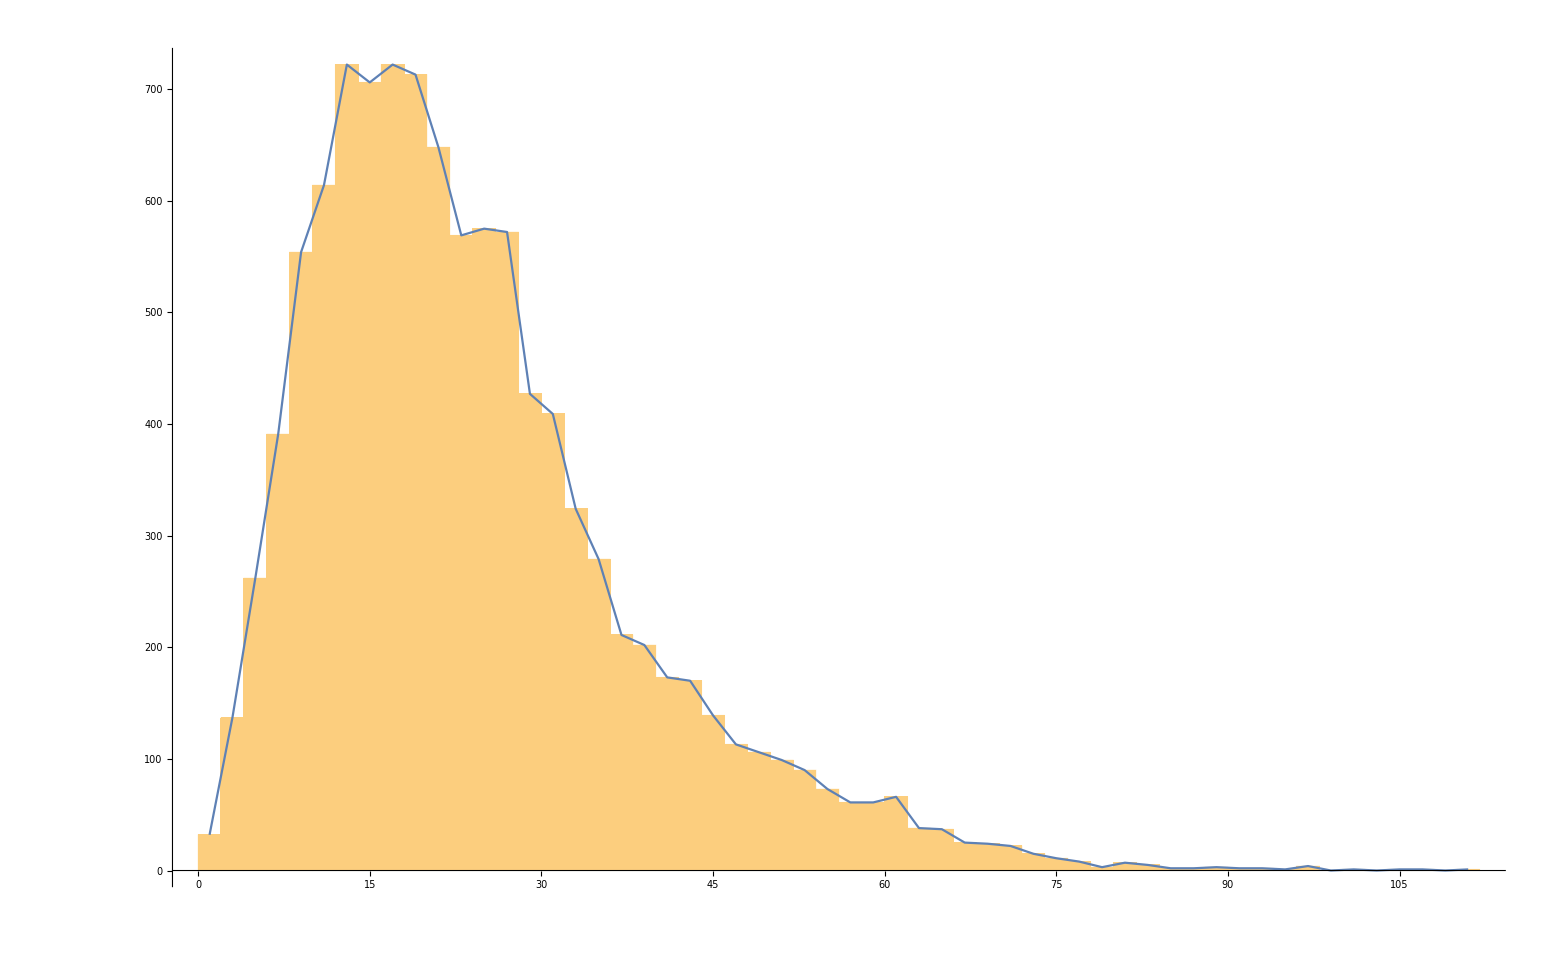

```mathematica
Show[g,ListLinePlot[Thread[{Table[i,{i,1,112,2}],Flatten[binCounts]}]]]
```

# --------------------------------------------------------------D10 F6 M13 G1相应平均位置和方差

```mathematica
myteamfnpoistionmean1d10=Table[Mean[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_D"<>ToString[x],_,_,_,_,_}]]
,{x,1,10}]//N
```

{{34.2973,54.0834},{34.7431,45.1638},{35.4677,51.5667},{50.7188,12.5255},{48.3248,34.8624},{39.3199,75.6398},{51.1152,82.7353},{51.9962,86.7985},{35.5965,30.5965},{37.1842,21.9737}}

```mathematica
myteamfnpoistionmean2d10=Table[Mean[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_D"<>ToString[x],_,_,_,_}]]
,{x,1,10}]//N
```

{{35.3009,54.5855},{36.1199,44.242},{36.701,51.3832},{53.4439,10.5138},{52.1532,36.5077},{42.7309,78.2263},{54.8931,85.5011},{56.6341,87.9617},{42.878,28.9024},{37.129,23.2903}}

```mathematica
myteamfnpoistionvariance1d10=Table[Sqrt/@Variance[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_D"<>ToString[x],_,_,_,_,_}]]
,{x,1,10}]//N
```

{{13.082,24.2677},{12.7291,19.9855},{13.2383,24.4423},{19.5135,11.3201},{21.0428,34.8681},{16.6059,14.4557},{21.39,18.6876},{21.8846,11.5366},{13.7579,15.732},{13.0526,17.6367}}

```mathematica
myteamfnpoistionvariance2d10=Table[Sqrt/@Variance[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_D"<>ToString[x],_,_,_,_}]]
,{x,1,10}]//N
```

{{12.9702,23.5538},{13.2805,19.1579},{13.936,24.9247},{19.3998,9.24368},{21.4411,37.1711},{18.1001,14.9735},{21.4888,18.6902},{21.8668,9.82657},{19.7853,12.9476},{13.679,17.2341}}

```mathematica
myteamfnpoistionmean1m13=Table[Mean[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_M"<>ToString[x],_,_,_,_,_}]]
,{x,1,13}]//N
```

{{49.7179,52.6175},{53.8947,47.3026},{46.7035,46.3957},{55.2354,55.833},{58.4524,42.881},{57.5689,35.1299},{48.3182,56.5455},{58.8759,72.5839},{63.0538,57.8692},{59.6389,52.1111},{50.5385,53.6462},{63.3806,28.1045},{53.3378,52.6486}}

```mathematica
myteamfnpoistionmean2m13=Table[Mean[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_M"<>ToString[x],_,_,_,_}]]
,{x,1,13}]//N
```

{{50.7807,52.2271},{57.3043,49.0435},{46.6123,46.3473},{58.3129,54.5048},{62.9024,43.439},{61.5903,34.9404},{51.6667,59.5556},{63.887,73.2316},{63.5704,58.1338},{59.1,49.15},{51.38,56.42},{66.307,29.8791},{56.7018,42.8246}}

```mathematica
myteamfnpoistionvariance1m13=Table[Sqrt/@Variance[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_M"<>ToString[x],_,_,_,_,_}]]
,{x,1,13}]//N
```

{{15.8945,24.3758},{18.5663,26.4963},{15.2237,21.9129},{18.3739,25.1401},{17.1311,26.8385},{18.2609,24.0256},{12.0491,16.6096},{19.7206,26.217},{19.4312,28.7293},{17.0933,30.3567},{16.3297,21.3245},{17.9296,26.2808},{14.3539,24.031}}

```mathematica
myteamfnpoistionvariance2m13=Table[Sqrt/@Variance[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_M"<>ToString[x],_,_,_,_}]]
,{x,1,13}]//N
```

{{15.4573,23.0698},{18.1564,27.2388},{14.1988,21.1888},{18.2215,24.9661},{16.5617,26.9203},{18.1299,23.6023},{13.0113,14.7338},{17.6821,26.1003},{18.6454,28.9539},{18.9585,31.8454},{14.4136,17.7478},{17.917,28.2228},{13.6185,24.8202}}

```mathematica
myteamfnpoistionmean1f6=Table[Mean[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_F"<>ToString[x],_,_,_,_,_}]]
,{x,1,6}]//N
```

{{65.8697,48.1933},{53.7218,48.1874},{60.3571,55.0179},{69.504,49.144},{66.4937,42.1835},{62.4574,69.7578}}

```mathematica
myteamfnpoistionmean2f6=Table[Mean[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_F"<>ToString[x],_,_,_,_}]]
,{x,1,6}]//N
```

{{68.2516,47.4651},{55.3474,47.9461},{66.4521,49.9178},{72.2907,46.8893},{68.8117,42.1121},{68.7288,72.061}}

```mathematica
myteamfnpoistionvariance1f6=Table[Sqrt/@Variance[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_F"<>ToString[x],_,_,_,_,_}]]
,{x,1,6}]//N
```

{{18.384,31.9445},{16.2411,23.6906},{16.3367,28.1079},{16.8181,29.4346},{15.7952,27.7151},{19.356,26.3547}}

```mathematica
myteamfnpoistionvariance2f6=Table[Sqrt/@Variance[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_F"<>ToString[x],_,_,_,_}]]
,{x,1,6}]//N
```

{{15.8021,28.7393},{16.8802,24.1733},{15.1612,29.1384},{15.4146,28.2092},{16.3115,26.7336},{17.9582,26.2149}}

```mathematica
myteamfnpoistionmean1g1=Table[Mean[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_G"<>ToString[x],_,_,_,_,_}]]
,{x,1,1}]//N
```

{{12.1776,48.3129}}

```mathematica
myteamfnpoistionvariance1g1=Table[Sqrt/@Variance[Take[#,{4,5}]&/@Cases[myteam,{"Huskies","Huskies_G"<>ToString[x],_,_,_,_,_}]]
,{x,1,1}]//N
```

{{4.82074,11.6808}}

```mathematica
myteamfnpoistionvariance2g1=Table[Sqrt/@Variance[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_G"<>ToString[x],_,_,_,_}]]
,{x,1,1}]//N
```

{{8.8759,13.7012}}

```mathematica
myteamfnpoistionmean2g1=Table[Mean[Take[#,{6,7}]&/@Cases[myteam,{"Huskies",_,"Huskies_G"<>ToString[x],_,_,_,_}]]
,{x,1,1}]//N
```

{{11.2661,46.4556}}

# ---------------------------------------------------------------------------------------顶点配置

# -------------------------------------------------------------------------对应顶点位置、方差数据处理

```mathematica
StringReplace[{"Huskies_D1","Huskies_D10","Huskies_D2","Huskies_D3","Huskies_D4","Huskies_D5","Huskies_D6","Huskies_D7","Huskies_D8","Huskies_D9","Huskies_F1","Huskies_F2","Huskies_F3","Huskies_F4","Huskies_F5","Huskies_F6","Huskies_G1","Huskies_M1","Huskies_M10","Huskies_M11","Huskies_M12","Huskies_M13","Huskies_M2","Huskies_M3","Huskies_M4","Huskies_M6","Huskies_M7","Huskies_M8","Huskies_M9","Huskies_M5"},{"H"->"h","_"->""}];
```

```mathematica
huskiesF=(myteamfnpoistionmean1f6+myteamfnpoistionmean2f6)/2
```

{{67.0607,47.8292},{54.5346,48.0667},{63.4046,52.4678},{70.8973,48.0166},{67.6527,42.1478},{65.5931,70.9094}}

```mathematica
huskiesD=(myteamfnpoistionmean1d10+myteamfnpoistionmean2d10)/2
```

{{34.7991,54.3345},{35.4315,44.7029},{36.0844,51.4749},{52.0814,11.5197},{50.239,35.6851},{41.0254,76.933},{53.0041,84.1182},{54.3152,87.3801},{39.2373,29.7495},{37.1566,22.632}}

```mathematica
huskiesM=(myteamfnpoistionmean1m13+myteamfnpoistionmean2m13)/2
```

{{50.2493,52.4223},{55.5995,48.1731},{46.6579,46.3715},{56.7741,55.1689},{60.6774,43.16},{59.5796,35.0352},{49.9924,58.0505},{61.3815,72.9078},{63.3121,58.0015},{59.3694,50.6306},{50.9592,55.0331},{64.8438,28.9918},{55.0198,47.7366}}

```mathematica
huskiesG=(myteamfnpoistionmean1g1+myteamfnpoistionmean2g1)/2
```

{{11.7219,47.3843}}

```mathematica
huskiesFvariance=(myteamfnpoistionvariance1f6+myteamfnpoistionvariance2f6)/2
```

{{17.093,30.3419},{16.5606,23.9319},{15.749,28.6232},{16.1164,28.8219},{16.0533,27.2243},{18.6571,26.2848}}

```mathematica
huskiesDvariance=(myteamfnpoistionvariance1d10+myteamfnpoistionvariance2d10)/2
```

{{13.0261,23.9107},{13.0048,19.5717},{13.5872,24.6835},{19.4566,10.2819},{21.2419,36.0196},{17.353,14.7146},{21.4394,18.6889},{21.8757,10.6816},{16.7716,14.3398},{13.3658,17.4354}}

```mathematica
huskiesMvariance=(myteamfnpoistionvariance1m13+myteamfnpoistionvariance2m13)/2
```

{{15.6759,23.7228},{18.3614,26.8676},{14.7113,21.5509},{18.2977,25.0531},{16.8464,26.8794},{18.1954,23.8139},{12.5302,15.6717},{18.7014,26.1587},{19.0383,28.8416},{18.0259,31.1011},{15.3716,19.5361},{17.9233,27.2518},{13.9862,24.4256}}

```mathematica
huskiesGvariance=(myteamfnpoistionvariance1g1+myteamfnpoistionvariance2g1)/2
```

{{6.84832,12.691}}

# -----校对顶点 (先画图)

```mathematica
graph30=Graph[Rule@@@myteamperfect,VertexLabels->Placed["Name",{1/2,1/2}],
Background->None];
```

```mathematica
graph30simple=Graph[Union[Rule@@@myteamperfect],VertexLabels->Placed["Name",{1/2,1/2}],
Background->None];
```

```mathematica
VertexList[graph30simple]
```

{Huskies_D1,Huskies_D10,Huskies_D2,Huskies_D3,Huskies_D4,Huskies_D5,Huskies_D6,Huskies_D7,Huskies_D8,Huskies_D9,Huskies_F1,Huskies_F2,Huskies_F3,Huskies_F4,Huskies_F5,Huskies_F6,Huskies_G1,Huskies_M1,Huskies_M10,Huskies_M11,Huskies_M12,Huskies_M13,Huskies_M2,Huskies_M3,Huskies_M4,Huskies_M6,Huskies_M7,Huskies_M8,Huskies_M9,Huskies_M5}

```mathematica
vertexlist={"Huskies_D1","Huskies_D10","Huskies_D2","Huskies_D3","Huskies_D4","Huskies_D5","Huskies_D6","Huskies_D7","Huskies_D8","Huskies_D9","Huskies_F1","Huskies_F2","Huskies_F3","Huskies_F4","Huskies_F5","Huskies_F6","Huskies_G1","Huskies_M1","Huskies_M10","Huskies_M11","Huskies_M12","Huskies_M13","Huskies_M2","Huskies_M3","Huskies_M4","Huskies_M6","Huskies_M7","Huskies_M8","Huskies_M9","Huskies_M5"};
```

```mathematica
vertexmeanlist={huskiesD[[1]],huskiesD[[10]],huskiesD[[2]],huskiesD[[3]],huskiesD[[4]],huskiesD[[5]],huskiesD[[6]],huskiesD[[7]],huskiesD[[8]],huskiesD[[9]],huskiesF[[1]],huskiesF[[2]],huskiesF[[3]],huskiesF[[4]],huskiesF[[5]],huskiesF[[6]],huskiesG[[1]],huskiesM[[1]],huskiesM[[10]],huskiesM[[11]],huskiesM[[12]],huskiesM[[13]],huskiesM[[2]],huskiesM[[3]],huskiesM[[4]],huskiesM[[6]],huskiesM[[7]],huskiesM[[8]],huskiesM[[9]],huskiesM[[5]]};
```

```mathematica
vertexvariancelist={huskiesDvariance[[1]],huskiesDvariance[[10]],huskiesDvariance[[2]],huskiesDvariance[[3]],huskiesDvariance[[4]],huskiesDvariance[[5]],huskiesDvariance[[6]],huskiesDvariance[[7]],huskiesDvariance[[8]],huskiesDvariance[[9]],huskiesFvariance[[1]],huskiesFvariance[[2]],huskiesFvariance[[3]],huskiesFvariance[[4]],huskiesFvariance[[5]],huskiesFvariance[[6]],huskiesGvariance[[1]],huskiesMvariance[[1]],huskiesMvariance[[10]],huskiesMvariance[[11]],huskiesMvariance[[12]],huskiesMvariance[[13]],huskiesMvariance[[2]],huskiesMvariance[[3]],huskiesMvariance[[4]],huskiesMvariance[[6]],huskiesMvariance[[7]],huskiesMvariance[[8]],huskiesMvariance[[9]],huskiesMvariance[[5]]};
```

```mathematica
VertexSizeList=(Part[#,1]^2+Part[#,2]^2)&/@vertexvariancelist//Sqrt
```

{27.2287,21.969,23.4984,28.176,22.0063,41.8166,22.7519,28.4416,24.3442,22.0662,34.8253,29.1031,32.6698,33.0218,31.605,32.2332,14.4208,28.4342,35.9473,24.8585,32.6176,28.1465,32.5424,26.0933,31.0236,29.9696,20.0651,32.1561,34.5586,31.7223}

```mathematica
VertexSizeListNew=(VertexSizeList-Min[VertexSizeList])/(Max[VertexSizeList]-Min[VertexSizeList])/1.2+0.1
```

{0.489594,0.329603,0.376124,0.518407,0.330737,0.933333,0.353415,0.526487,0.401853,0.332559,0.72067,0.54661,0.655102,0.66581,0.622712,0.641822,0.1,0.526263,0.754799,0.417497,0.653513,0.51751,0.651226,0.455057,0.605028,0.572967,0.271688,0.639477,0.712555,0.62628}

# --------------------------------------------------------------画图

```mathematica
EdgeList[graph30simple];
```

```mathematica
Thread[Table["Huskies_D"<>ToString[x],{x,1,10}]->Blue]
```

{Huskies_D1→RGBColor[0, 0, 1],Huskies_D2→RGBColor[0, 0, 1],Huskies_D3→RGBColor[0, 0, 1],Huskies_D4→RGBColor[0, 0, 1],Huskies_D5→RGBColor[0, 0, 1],Huskies_D6→RGBColor[0, 0, 1],Huskies_D7→RGBColor[0, 0, 1],Huskies_D8→RGBColor[0, 0, 1],Huskies_D9→RGBColor[0, 0, 1],Huskies_D10→RGBColor[0, 0, 1]}

# -------------------关系对应边权重

```mathematica
Thread[VertexList[graph30]->VertexDegree[graph30]]
```

{Huskies_D1→1525,Huskies_F1→709,Huskies_M1→2258,Huskies_F2→1776,Huskies_M2→141,Huskies_M3→1604,Huskies_G1→965,Huskies_D2→1043,Huskies_D3→1299,Huskies_D4→1180,Huskies_F3→129,Huskies_D5→1194,Huskies_M4→1002,Huskies_M5→81,Huskies_D6→645,Huskies_M6→1039,Huskies_M7→40,Huskies_M8→312,Huskies_M9→272,Huskies_F4→408,Huskies_D7→855,Huskies_M10→76,Huskies_M11→115,Huskies_M12→345,Huskies_M13→129,Huskies_F5→379,Huskies_F6→518,Huskies_D8→548,Huskies_D9→98,Huskies_D10→69}

```mathematica
{"Huskies_D1","Huskies_F1"}->23/.{a_,b_}->{a->b}
```

{Huskies_D1→Huskies_F1}→23

```mathematica
countsmyteamfn1=Normal[Counts[myteamfn2]]/.{{a_,b_}->{a->b}};
```

```mathematica
countsmyteamfn2=#/.List->Identity&/@countsmyteamfn1;
```

```mathematica
"Huskies_D1"->"Huskies_F1"->23/.x_Integer->AbsoluteThickness[x]
```

Huskies_D1->Huskies_F1→AbsoluteThickness[23]

```mathematica
countsmyteamfn3=countsmyteamfn2/.x_Integer->AbsoluteThickness[x/20];
```

```mathematica
countsmyteamfn3;
```

```mathematica
{"Huskies_D1"->"Huskies_D1"}/.countsmyteamfn1
```

{Huskies_D1->Huskies_D1}

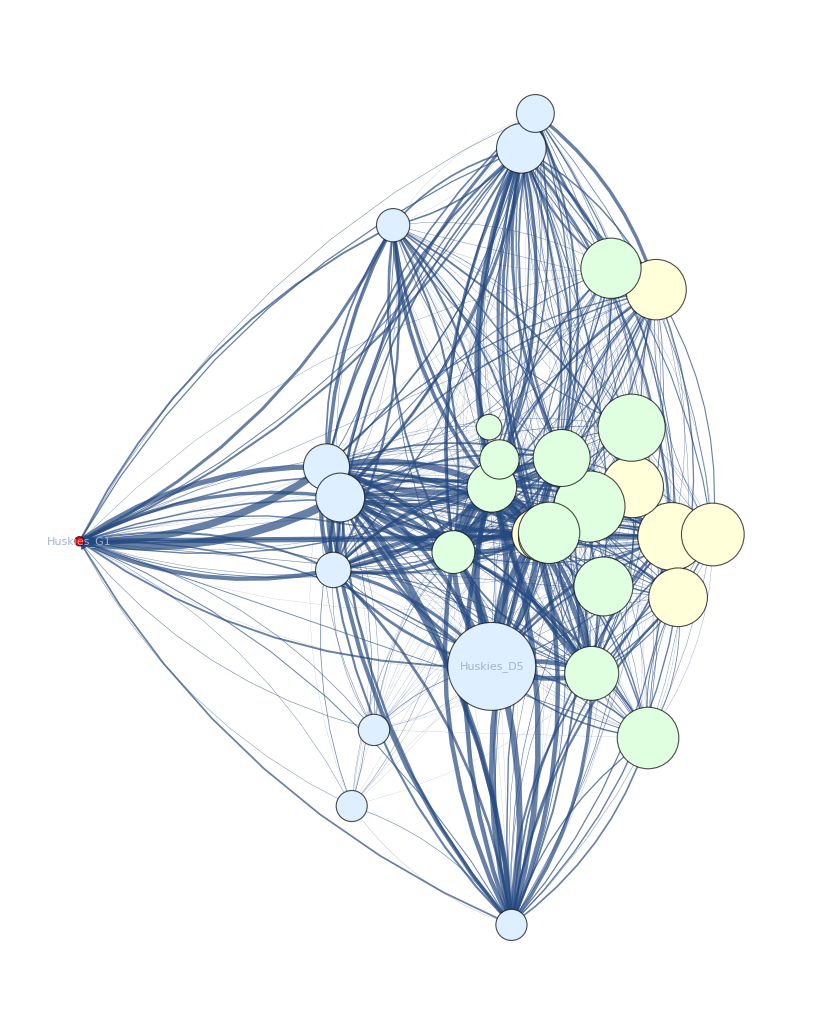

```mathematica
graph30simple=Graph[Union[Rule@@@myteamperfect],VertexLabels->Thread[{"Huskies_D5","Huskies_G1"}->Placed["Name",{1/2,1/2}]],

VertexCoordinates->vertexmeanlist,
VertexSize->Thread[vertexlist->VertexSizeListNew*15],
EdgeStyle->countsmyteamfn3,
VertexStyle->Thread[Table["Huskies_D"<>ToString[x],{x,1,10}]->LightBlue]~Join~Thread[Table["Huskies_M"<>ToString[x],{x,1,13}]->LightGreen]~Join~Thread[Table["Huskies_F"<>ToString[x],{x,1,6}]->LightYellow]~Join~Thread[Table["Huskies_G"<>ToString[x],{x,1,1}]->Red],

Background->None]
```

```mathematica
Export["example.png",graph30simple,ImageResolution->300]
```

example.png

```mathematica
SystemOpen["example.png"]
```

```mathematica
FindIndependentVertexSet[graph30simple]
```

{{Huskies_D10,Huskies_D8,Huskies_D9,Huskies_M10,Huskies_M13,Huskies_M7,Huskies_M5}}

```mathematica
HighlightGraph[graph30simple,%,GraphHighlightStyle->"Thick"];
```

# ---------------------传球次数

```mathematica
passnumber=VertexDegree[graph30]
```

{1525,709,2258,1776,141,1604,965,1043,1299,1180,129,1194,1002,81,645,1039,40,312,272,408,855,76,115,345,129,379,518,548,98,69}

```mathematica
Variance[passnumber]//Sqrt//N
```

596.4

# ---------------------核心球员

```mathematica
coremumber=Select[Abs[passnumber-Mean[passnumber]],#>Sqrt[Variance[passnumber]]&]//N
```

{833.2,1566.2,1084.2,912.2,607.2,610.8,651.8,615.8,622.8}

```mathematica
Variance[coremumber]//Sqrt//N
```

322.394

# --------------------------三/四元图

```mathematica
possible=Subsets[vertexlist,{3}];
```

```mathematica
possible//Length
```

4060

```mathematica
smallgraph=Sort[Subgraph[graph30simple,#,GraphLayout->"CircularEmbedding"]&/@possible,IsomorphicGraphQ];
```

```mathematica
smallgraph//Length
```

4060

```mathematica
pattern=Union[smallgraph,SameTest->(IsomorphicGraphQ[#1,#2]&)];
```

```mathematica
pattern//Length
```

16

```mathematica
Table[Length[Select[smallgraph,IsomorphicGraphQ[#,pattern[[i]]]&]],{i,1,16}];
```

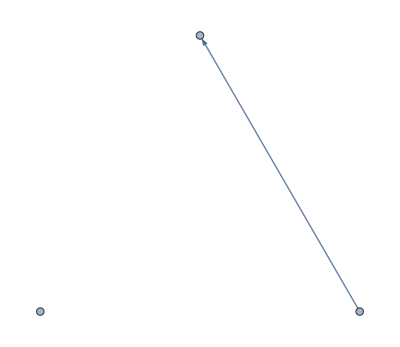
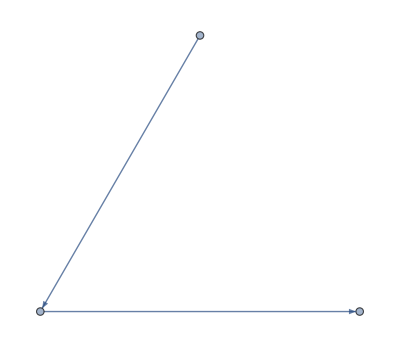
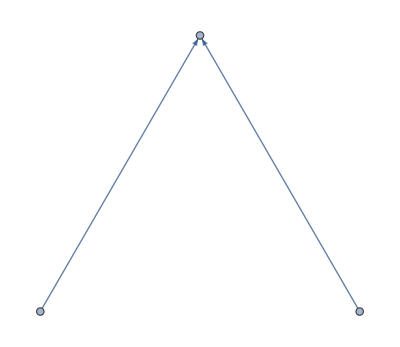
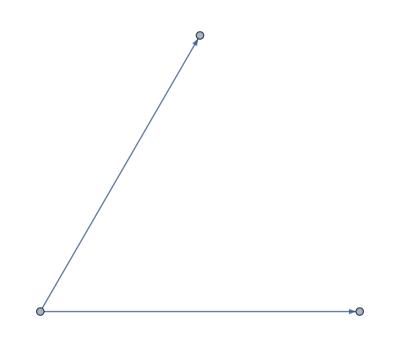
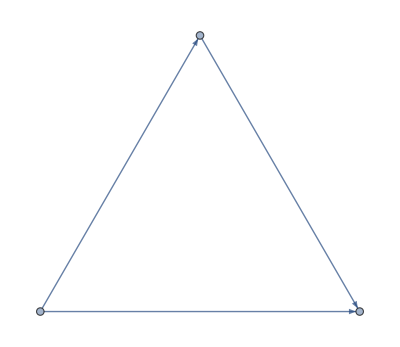
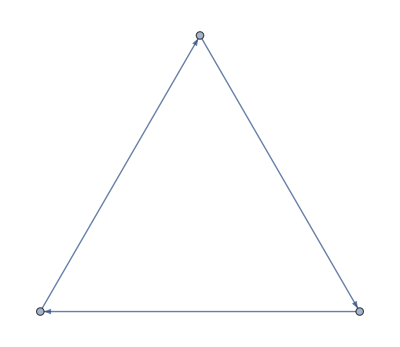
<|-Graphics-→1542,-Graphics-→795,-Graphics-→603,-Graphics-→379,-Graphics-→178,-Graphics-→155,-Graphics-→119,-Graphics-→118,-Graphics-→40,-Graphics-→37,-Graphics-→31,-Graphics-→29,-Graphics-→12,-Graphics-→10,-Graphics-→8,-Graphics-→4|>

```mathematica
Sort[Association[Thread[pattern->Table[Length[Select[smallgraph,IsomorphicGraphQ[#,pattern[[i]]]&]],{i,1,16}]]],Greater]
```

```mathematica
#[[]]{-Graphics-->1542,-Graphics-->795,-Graphics-->603,-Graphics-->379,-Graphics-->178,-Graphics-->155,-Graphics-->119,-Graphics-->118,-Graphics-->40,-Graphics-->37,-Graphics-->31,-Graphics-->29}
```

```mathematica
possible2=Subsets[vertexlist,{4}];
```

```mathematica
possible2//Length
```

27405

```mathematica
smallgraph2=Sort[Subgraph[graph30simple,#,GraphLayout->"CircularEmbedding"]&/@possible2,IsomorphicGraphQ];
```

```mathematica
smallgraph2//Length
```

27405

```mathematica
pattern2=Union[smallgraph2,SameTest->(IsomorphicGraphQ[#1,#2]&)];
```

```mathematica
pattern2//Length
```

179

```mathematica
Table[Length[Select[smallgraph2,IsomorphicGraphQ[#,pattern2[[i]]]&]],{i,1,179}];
```

```mathematica
Sort[Association[Thread[pattern2[[1;;16]]->Table[Length[Select[smallgraph,IsomorphicGraphQ[#,pattern[[i]]]&]],{i,1,16}]]],Greater]
```

<|-Graphics-→1542,-Graphics-→795,-Graphics-→603,-Graphics-→379,-Graphics-→178,-Graphics-→155,-Graphics-→119,-Graphics-→118,-Graphics-→40,-Graphics-→37,-Graphics-→31,-Graphics-→29,-Graphics-→12,-Graphics-→10,-Graphics-→8,-Graphics-→4|>

```mathematica
edgelistthick=EdgeList[graph30simple]/.countsmyteamfn2
```

{2,59,105,73,57,25,34,23,6,23,49,5,19,19,18,107,92,2,2,13,2,3,51,26,21,4,3,6,1,10,8,1,2,6,3,5,2,62,49,39,47,52,26,2,8,13,56,1,8,4,8,62,46,1,4,2,1,44,22,1,12,2,1,5,98,9,35,59,14,6,18,42,21,50,1,8,14,21,120,47,1,4,9,3,5,54,30,4,23,3,14,9,57,3,30,35,1,1,2,25,66,10,25,33,20,25,62,3,19,9,63,33,8,30,7,36,40,15,12,3,2,4,42,97,6,27,6,3,27,75,3,1,23,9,3,69,29,2,67,7,11,12,34,5,1,8,25,1,28,28,2,5,4,6,43,32,1,1,7,1,2,30,19,9,1,6,9,18,17,12,1,2,24,36,29,4,16,6,22,31,49,6,7,6,4,21,32,2,18,39,5,12,4,42,2,2,5,19,11,18,49,14,22,1,10,5,9,28,1,8,7,7,10,1,1,3,3,3,8,4,1,6,3,5,4,7,18,17,4,12,3,1,27,4,9,3,3,30,2,2,3,2,14,22,2,27,1,12,3,55,33,56,64,84,41,32,41,3,30,6,12,15,23,6,117,6,18,3,8,58,50,5,58,15,15,2,2,3,3,5,2,4,4,11,1,5,1,1,3,1,8,6,7,2,2,7,2,5,9,1,5,10,15,2,4,3,5,12,20,2,3,1,1,1,1,20,7,1,4,10,7,23,2,17,9,11,3,1,2,15,16,5,8,6,6,7,3,15,37,6,22,16,18,19,1,6,3,3,10,25,11,1,76,6,29,49,14,22,27,18,7,9,77,22,5,15,8,6,24,12,1,19,7,1,10,5,2,85,3,63,60,79,79,54,70,46,3,34,182,9,36,13,31,20,8,6,20,4,10,143,72,3,77,3,25,10,3,2,1,2,1,9,1,3,3,1,3,3,3,1,1,7,2,1,2,7,3,4,8,2,1,1,1,1,5,7,7,4,1,4,3,24,22,3,8,2,2,11,8,14,4,8,9,2,6,1,1,3,5,2,6,4,12,2,4,1,3,1,5,2,12,6,5,2,3,3,12,3,1,3,4,5,2,3,2,6,12,5,8,74,6,46,56,88,67,28,44,22,3,21,63,4,13,12,16,12,168,4,1,28,8,7,27,3,44,11,11,30,1,26,18,28,23,10,41,25,2,20,50,3,12,6,16,5,71,6,3,7,3,26,4,34,14,5,1,2,3,4,4,3,7,2,1,3,4,1,4,2,16,13,12,50,71,4,20,1,40,52,6,24,14,14,1,54,2,4,12,4,4,28,24,1,4,15,15,3,1,3,1,3,2,2,5,2,1,2,9,1,5,3,31,14,18,4,1,1,20,1,3,6,7,4,3,2,4,2,4,10,10,14,7,7,4,9,4,4,1,11,1,2,5,8,6,15,2}

```mathematica
FindClique[graph30simple,Infinity,All];
```

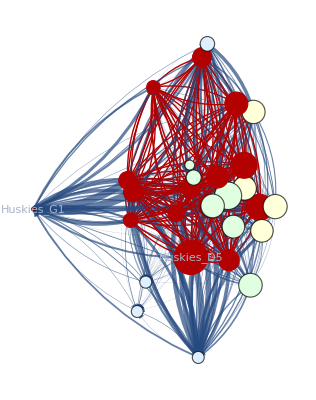
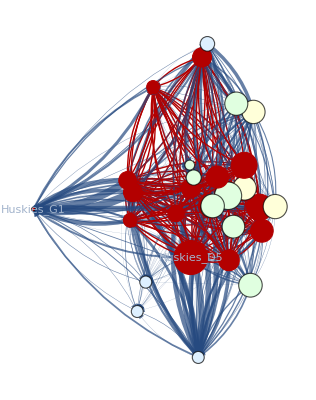
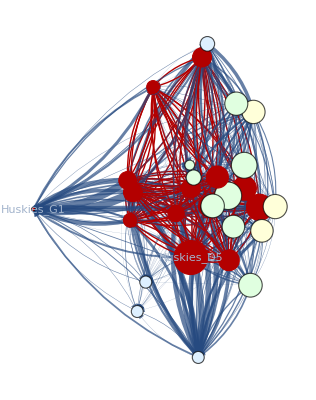

```mathematica
Table[HighlightGraph[graph30simple,Subgraph[graph30simple,clique]],{clique,FindClique[graph30simple,∞,3]}]
```

```mathematica
ToString[{"Huskies_D1","Huskies_F1"}->23]
```

{Huskies_D1, Huskies_F1} -> 23

```mathematica
"{Huskies_D1, Huskies_F1} -> 23"
```

{Huskies_D1, Huskies_F1} -> 23